## First part

```mathematica
WebImageSearch["Resistor", "Thumbnails"]
```

$Aborted

```mathematica
ColorQuantize[-Graphics-,14]
```

-Graphics-

```mathematica
ColorQuantize[ColorConvert[-Graphics-,"CMYK"],14]
```

-Graphics-

```mathematica
Map[ColorQuantize[#,14]&,WebImageSearch["Resistor", "Thumbnails"]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
pictures = WebImageSearch["resistor","Thumbnails"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
img = -Graphics-;
saturated = Binarize[ColorConvert[img, "Grayscale"], .9]
Inpaint[img, Dilation[saturated, DiskMatrix[20]]]
```

-Graphics-

$Aborted

```mathematica
ClearAll[a]
```

```mathematica
ColorQuantize[-Graphics-, 10]
```

-Graphics-

```mathematica
MorphologicalComponents[-Graphics-]//Colorize
```

-Graphics-

```mathematica
lenet=NetChain[
{
ConvolutionLayer[20,5],
Ramp,
PoolingLayer[2,2],
ConvolutionLayer[50,5],
Ramp,
PoolingLayer[2,2],
FlattenLayer[],
500,
Ramp,
10,
SoftmaxLayer[]
},
"Output"->NetDecoder[{"Class",Range[0,9]}],"Input"->NetEncoder[{"Image",{28,28},"Grayscale"}]
]
```

```mathematica
ImageIdentify[-Graphics-]
```

resistor

```mathematica
Entity["Concept","Resistor::d7w57"]["Properties"]
```

{alternate names,broader concepts,definition,equivalent entity,name,narrower concepts,similar entities,subset concepts,superset concepts,WordData senses,WordNet ID}

```mathematica
ImageAlign[-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
WebImageSearch["Resistor","Images","MaxItems"->1]
```

{-Graphics-}

```mathematica
DeleteSmallComponents @ChanVeseBinarize[-Graphics-]
```

-Graphics-

```mathematica
HistogramTransform @ ImageAdjust[-Graphics-]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {0}.

-Graphics-

```mathematica
ColorQuantize[ImageAdjust[-Graphics-,1],14]
```

-Graphics-

```mathematica
EdgeDetect[-Graphics-]
```

-Graphics-

```mathematica
CrossingDetect[-Graphics-]
```

-Graphics-

```mathematica
ContourDetect[-Graphics-]
```

-Graphics-

```mathematica
img = -Graphics-;
lines = ImageLines[img];
HighlightImage[img, {Orange, Line /@ lines}]
```

-Graphics-

```mathematica
GradientFilter[-Graphics-,1]
```

-Graphics-

```mathematica
img = -Graphics-;
lines = ImageLines[img];
HighlightImage[img, {Orange, Line /@ lines}]
```

-Graphics-

```mathematica
LaplacianGaussianFilter[-Graphics-,1]
```

-Graphics-

```mathematica
img = EdgeDetect[-Graphics-]
lines = ImageLines[img];
HighlightImage[img, {Orange, Line /@ lines}]
```

-Graphics-

-Graphics-

```mathematica
Entity["AdministrativeDivision",{"Massachusetts","UnitedStates"}]["Polygon"]
```

Massachusetts, United States

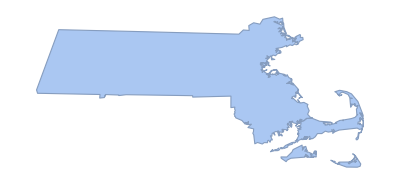

```mathematica
BoundaryDiscretizeGraphics[Entity["AdministrativeDivision",{"Massachusetts","UnitedStates"}]["Polygon"]]
```

## First method to orient the resistor

```mathematica
prepareImage[img_Image] := Module[{imgwbg, mag, ori, nbins, mat, total, angle},

    imgwbg = RemoveBackground[img];
    
    mag = GradientFilter[imgwbg, 1];

    ori = GradientOrientationFilter[imgwbg, 1, Method -> {"UndefinedOrientationValue" -> 0}];
    
    nbins = 180;

    mat = ImageCooccurrence[{mag, ImageAdjust[ori, {0,0,1}, π/2 * {-1,1}]},
          nbins, {{1}}];

    total = Total[ mat * Range[0, 1-1/nbins, 1/nbins]];

    angle = Pi/2(1-(Position[total, Max[total]][[1,1]]-1/2)/(nbins/2));
    
    ImageRotate[imgwbg, angle, Masking->Full]
    

 ];
```

## Getting the samples

```mathematica
img = -Graphics-;
imgarr = ImagePartition[img, {ImageDimensions[img][[1]],ImageDimensions[img][[2]]/13 }];
arr10omh = Map[RemoveAlphaChannel[prepareImage[#]]&,Flatten @ imgarr];
```

```mathematica
img = -Graphics-;
imgarr = ImagePartition[img, {ImageDimensions[img][[1]]/14 ,ImageDimensions[img][[2]]}];
arr220Komh = Map[RemoveAlphaChannel[prepareImage[#]]&,Flatten @ imgarr];
```

```mathematica
img = -Graphics-;
imgarr = ImagePartition[img, {ImageDimensions[img][[1]]/13 ,ImageDimensions[img][[2]]}];
arr4p7KKomh = Map[RemoveAlphaChannel[prepareImage[#]]&,Flatten @ imgarr];
```

```mathematica
c =Classify[<|"10"->Take[arr10omh,10], "220K"->Take[arr220Komh,10], "4.7K"->Take[arr4p7KKomh,10]|>, Method->"NeuralNetwork"]
```

ClassifierFunction[…]

```mathematica
c[Part[arr4p7KKomh,13],"Probabilities"]
```

<|10→0.00652864,220K→0.00724117,4.7K→0.98623|>

```mathematica
img = -Graphics-;
imgarr = ImagePartition[img, {ImageDimensions[img][[1]]/14 ,ImageDimensions[img][[2]]}];
arr220KTest = Map[RemoveAlphaChannel[prepareImage[#]]&,Flatten @ imgarr]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
c[%1562[[1]], "Probabilities"]
```

<|10→0.997887,220K→0.00088973,4.7K→0.00122279|>

## From article

```mathematica
img = -Graphics-;
img = -Graphics-;
img = ImageAdjust[ImageResize[img, {500}]];
img = ColorConvert[RemoveAlphaChannel[img],"RGB"]
```

-Graphics-

```mathematica
meanColorMask[image_,mask_ ]:= Module[
{toRemove,imgList},
toRemove = PixelValuePositions[mask, Black];
imgList = Transpose @ ImageData[image];
imgList = Delete[imgList, toRemove];
RGBColor[Mean[Catenate @ imgList]]
]
```

```mathematica
(*getBackColor[image_] := Module[
{edge},
	edge = ImageCrop[image,{10,10},{Right,Bottom}];
	RGBColor [Mean @ Catenate[ImageData[edge]]]
]*)
getBackColor[image_] := meanColorMask[image, ColorNegate @ AlphaChannel[RemoveBackground[image]]];
backColor = getBackColor[img]
```

RGBColor[{0.4647289741747594, 0.46767765548741147, 0.4936690884215208}]

```mathematica
absoluteSubstract[image_, color_] := ImageApply[
	MapThread[
		Abs[#1 - #2]&,
		{Flatten[#],Flatten[List @@ color]}
	]&,
	image
]
substracted = absoluteSubstract[img, backColor]
```

-Graphics-

```mathematica
monochromatic = ColorConvert[substracted,"Grayscale"]
```

-Graphics-

```mathematica
threshold[n_] := Module[
	{num, p, ω, μ, μT, maxK, maxσ, σ2B, temp, k},
	num = Total[n];
	p = n / num;
	ω := Sum[p[i],{i,0,#}]&;
	μ := Sum[(i+1) * p[i], {i, 0, #}]&;
	μT = μ[255];
	σ2B[x_Integer] := Module[
		{μk, ωk},
		ωk = ω[x];
		μk = μ[x];
		If[ ωk ≠ 0 && ωk ≠ 1,
			((μT*ωk - μk)^2) / (ωk * (1 - ωk)),
			-1
		]
	];
	maxσ = 0;
	maxK = 255;
	For[k = 0, k < 255, k++,
		temp = σ2B[k];
		If[ NumberQ[temp] && temp > maxσ,
			maxσ = temp;
			maxK = k;
		]
	];
	maxK
]
```

-Graphics-

58

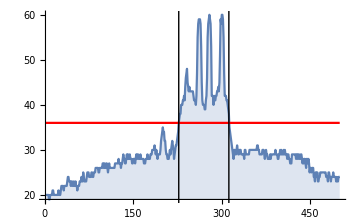
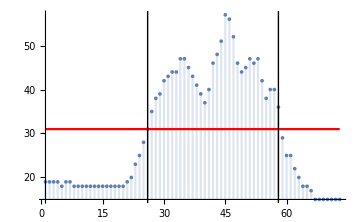
-Graphics- | -Graphics-
Horizontal mean | Vertical mean

-Graphics-

```mathematica
matr = ImageData[monochromatic];
verMean = Map[
	Mean[Flatten[#]]&,
	matr
];
verMean = Round[verMean * 255];
horMean = Map[
	Mean[Flatten[#]]&,
	Transpose[matr]
];
horMean = Round[horMean * 255];

horFrequency = Counts[Catenate[{horMean,Range[0,255]}]] - 1;
verFrequency = Counts[Catenate[{verMean,Range[0,255]}]] - 1;
verThreshold = threshold[verFrequency];
horThreshold = threshold[horFrequency];

verPlot = DiscretePlot[
	verMean[[x]],
	{x, 1, Length[verMean]},
	PlotRange->All,
	ImageSize->Medium
];
verThresholdPlot = Plot[
	verThreshold,
	{x, 1, Length[verMean]},
	PlotRange->All,
	ImageSize->Medium,
	PlotStyle->{Red}
];

horPlot = DiscretePlot[
	horMean[[x]],
	{x, 1, Length[horMean]},
	PlotRange->All,
	ImageSize->Medium
];
horThresholdPlot = Plot[
	horThreshold,
	{x, 1, Length[horMean]},
	PlotRange->All,
	ImageSize->Medium,
	PlotStyle->{Red}
];

xPos = Values @ Cases[
	MapIndexed[#1->First[#2]&, horMean],
	(x_->y_)/;x>= horThreshold
];
xStart = Min[xPos];
xEnd = Max[xPos];

yPos = Values @ Cases[
	MapIndexed[#1->First[#2]&, verMean],
	(x_->y_)/;x>= verThreshold
];
yStart = Min[yPos];
yEnd = Max[yPos];

segmented = ImageTake[
	img,
	{yStart, yEnd},{xStart, xEnd}
]
xStartLine = Graphics @ Line[{{xStart, 0},{xStart, 255}}];
xEndLine = Graphics @ Line[{{xEnd, 0},{xEnd, 255}}];
yStartLine = Graphics @ Line[{{yStart, 0},{yStart, 255}}];
yEndLine = Graphics @ Line[{{yEnd, 0},{yEnd, 255}}];
yEnd
Grid[{
	{
		Show[{horPlot, horThresholdPlot, xStartLine, xEndLine}],
		Show[{verPlot, verThresholdPlot, yStartLine, yEndLine}]
	},
	{"Horizontal mean", "Vertical mean"}
}]

extracted = ImageCrop[segmented, {ImageDimensions[segmented][[1]], 15}, Center]
```

### using morphological

```mathematica
extracted = ImageResize[extracted, {500}]
```

-Graphics-

```mathematica
exBackColor = 
ColorConvert[
	Hue @@ ImageMeasurements[ColorConvert[extracted, "HSB"], "Mean"],
	"RGB"
]
exSubs = 
TotalVariationFilter @ absoluteSubstract[
	extracted,
	ColorConvert[exBackColor,"RGB"]
]
exMono = ColorConvert[exSubs, "Grayscale"]
exBinary = Binarize[exMono,Method->"Cluster"]
allX = Map[
	Interval[{Ramp[Min[#]],Ramp[Max[#]]}]&,
	Values[ComponentMeasurements[
		MorphologicalComponents[exBinary],
		"MinimalBoundingBox"
	]][[All, All, 1]]
];
allX = List @@ (IntervalUnion @@ allX);
squaresX = Polygon @ Map[
	Module[
		{min, max, height},
		min = #[[1]];
		max = #[[2]];
		height = ImageDimensions[extracted][[2]];
		{{min, 1}, {min, height}, {max, height}, {max, 1}}
	]&,
	allX
];
HighlightImage[extracted, {Red, squaresX}]
```

RGBColor[0.23696657040633345, 0.2562154608969708, 0.17074789625041814]

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
ImageSaliencyFilter[-Graphics-, Method->"HistogramContrast"]//ImageAdjust
```

-Graphics-

```mathematica
HistogramTransform[extracted]
```

-Graphics-

```mathematica
EdgeDetect[extracted]
```

-Graphics-

### others

```mathematica
mainColor = getBackColor[extracted]
```

RGBColor[{0.2567064269079542, 0.20799858647406896, 0.17296709111053124}]

```mathematica
ClusteringComponents[ColorConvert[extracted,"LAB"],5,
 DistanceFunction->EuclideanDistance,
Method->"KMeans"
] // Colorize
```

-Graphics-

```mathematica
extractedSub = absoluteSubstract[extracted, mainColor]
```

-Graphics-

```mathematica
extractedMono = ColorConvert[extractedSub, "Grayscale"]
```

-Graphics-

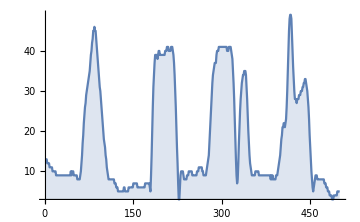

```mathematica
extractedMeans = Map[
	Mean[Flatten[#]]&,
	Transpose[ImageData[extractedMono]]
];
extractedMeans = Round[extractedMeans * 255];
extractedPlot = DiscretePlot[
	extractedMeans[[x]],
	{x, 1, Length[extractedMeans]},
	PlotRange->All,
	ImageSize->Medium
];
Show[{extractedPlot}]
```

```mathematica
img=-Graphics-;
lines=ImageLines[ImageAdjust@GradientFilter[img,3,Method->{"NonMaxSuppression"->True}],.09,Method->{"Segmented"->True}];
HighlightImage[img,{Yellow,Line/@lines}]
GradientFilter[img,3,Method->{"NonMaxSuppression"->True}]
```

-Graphics-

-Graphics-

## Dividing the image in sections

```mathematica
(*mask = Binarize[substracted]*)
mask =AlphaChannel[RemoveBackground[img]]
```

-Graphics-

```mathematica
PixelValuePositions[mask, Black]
```

{{1,73},{2,73},{3,73},{4,73},{5,73},{6,73},{7,73},{8,73},{9,73},{10,73},{11,73},{12,73},{13,73},{14,73},{15,73},{16,73},28397,{486,1},{487,1},{488,1},{489,1},{490,1},{491,1},{492,1},{493,1},{494,1},{495,1},{496,1},{497,1},{498,1},{499,1},{500,1}}
 |  |  |  |

```mathematica
meanColorMask[image_,mask_ ]:= Module[
{toRemove,imgList},
toRemove = PixelValuePositions[mask, Black];
imgList = Transpose @ ImageData[image];
imgList = Delete[imgList, toRemove];
RGBColor[Mean[Catenate @ imgList]]
]
```

```mathematica
maskColumns =First @ ImagePartition[mask, {10, ImageData[img][[1]]//Length}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
columns =First @ ImagePartition[img,{10, ImageData[img][[1]]//Length}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[meanColorMask[columns[[x]],maskColumns[[x]]],{x,Length[columns]}]
```

{RGBColor[{0.513033448673587, 0.5227220299884664, 0.5400560224089641}],RGBColor[{0.5195268189920599, 0.5287959812023986, 0.5456814130610925}],RGBColor[{0.5301307189542485, 0.5427777777777781, 0.5587254901960784}],RGBColor[{0.5405882352941179, 0.5541830065359478, 0.5726470588235294}],RGBColor[{0.5418954248366016, 0.5582352941176475, 0.574967320261438}],RGBColor[{0.5440522875816998, 0.5637908496732027, 0.5854575163398696}],RGBColor[{0.5518866370077443, 0.5660240566814961, 0.5879387048937224}],RGBColor[{0.55234297108674, 0.5696576935859091, 0.5872050515121303}],RGBColor[{0.553888888888889, 0.5732679738562096, 0.5948366013071897}],RGBColor[{0.5619281045751637, 0.57921568627451, 0.5970915032679739}],RGBColor[{0.5617647058823533, 0.5828104575163396, 0.6017320261437912}],RGBColor[{0.5756209150326799, 0.5951633986928103, 0.6123202614379085}],RGBColor[{0.5721895424836603, 0.5924836601307192, 0.6137908496732026}],RGBColor[{0.5781467425679951, 0.5952561669829223, 0.6213156230234028}],RGBColor[{0.5769934640522878, 0.595, 0.6178431372549019}],RGBColor[{0.5788299059461184, 0.5950263032042084, 0.6199585525267014}],RGBColor[{0.5867478025693036, 0.6018593644354293, 0.626707234617985}],RGBColor[{0.5906318082788672, 0.6006899055918664, 0.6261074800290486}],RGBColor[{0.5897544603426957, 0.5971736442324678, 0.6268503797915563}],RGBColor[{0.5853921568627451, 0.5945424836601307, 0.6288888888888884}],RGBColor[{0.5877684407096174, 0.5942421413009653, 0.626019296607532}],RGBColor[{0.5998764860274819, 0.6060830631465183, 0.6352014821676704}],RGBColor[{0.5928424516659812, 0.5996160702043052, 0.6300287947346769}],RGBColor[{0.5879009964641597, 0.5945869495339119, 0.62775956284153}],RGBColor[{0.5528594771241829, 0.55641339869281, 0.5833946078431367}],RGBColor[{0.5707869997313995, 0.5752027934461459, 0.6033736234219718}],RGBColor[{0.5830257029498017, 0.5903973319533096, 0.6173538036915647}],RGBColor[{0.5808304498269896, 0.5892964244521337, 0.6159515570934258}],RGBColor[{0.5744108919532204, 0.5860708675161466, 0.6078082271484256}],RGBColor[{0.5708110516934034, 0.5806038324420688, 0.6007464349376096}],RGBColor[{0.5787462027064347, 0.5885335542667777, 0.6077768572217617}],RGBColor[{0.5766909010795322, 0.5851656018212531, 0.6046706322978622}],RGBColor[{0.5694698620188821, 0.5800145243282502, 0.5982570806100219}],RGBColor[{0.5724585218702863, 0.5850075414781299, 0.6014479638009048}],RGBColor[{0.574932126696833, 0.587511312217195, 0.603469079939668}],RGBColor[{0.5761387631975867, 0.5890196078431374, 0.6059426847662142}],RGBColor[{0.5738150378261541, 0.5846225104214916, 0.6017600741083833}],RGBColor[{0.5740549019607842, 0.5827450980392156, 0.5961098039215689}],RGBColor[{0.5691789215686277, 0.57827818627451, 0.5922487745098041}],RGBColor[{0.569934640522876, 0.5827575474634299, 0.5947712418300654}],RGBColor[{0.5628248047186358, 0.5783197831978323, 0.5904989638131674}],RGBColor[{0.558566377370621, 0.5725490196078434, 0.581870781099325}],RGBColor[{0.5557843137254905, 0.5650326797385623, 0.5711437908496735}],RGBColor[{0.558612866634257, 0.5660670879922219, 0.5746556473829202}],RGBColor[{0.5483554712207466, 0.5570208728652752, 0.5665717900063254}],RGBColor[{0.5414588235294119, 0.5508078431372551, 0.5580862745098041}],RGBColor[{0.540423529411765, 0.5503058823529415, 0.5574901960784318}],RGBColor[{0.5340849673202616, 0.5385294117647063, 0.5462418300653596}],RGBColor[{0.5251960784313731, 0.5316993464052289, 0.5399019607843136}],RGBColor[{0.5267973856209153, 0.5335947712418304, 0.5418954248366015}]}

```mathematica
resistorBackColor = meanColorMask[img, mask]
```

RGBColor[{0.5665194620960401, 0.577068151343793, 0.5975184127169441}]

```mathematica
Table[RGBColor @ Mean[Catenate[ImageData[columns[[x]]]]],{x,Length[columns]}]
```

{RGBColor[{0.4574536663980645, 0.46638732205210737, 0.4790760139672315}],RGBColor[{0.46066075745366525, 0.4697663174858965, 0.4836583400483498}],RGBColor[{0.4711899006177807, 0.48209508460918765, 0.4967767929089457}],RGBColor[{0.47406392694063737, 0.486994359387595, 0.5033037872683311}],RGBColor[{0.4798979317754522, 0.4929948965887739, 0.5091216760676839}],RGBColor[{0.48602739726027616, 0.5010475423045946, 0.5174106903035162}],RGBColor[{0.4930808487778707, 0.5061026054257317, 0.5240021488047238}],RGBColor[{0.4934085414987937, 0.5076497448294375, 0.5247542304593058}],RGBColor[{0.5037818963201722, 0.5209024979854917, 0.5375288745635257}],RGBColor[{0.5069191512221342, 0.5228364222401263, 0.5401933924254639}],RGBColor[{0.5134085414987899, 0.5305345151759315, 0.5494816008595242}],RGBColor[{0.5236314799892532, 0.5402847166263763, 0.5552403975288777}],RGBColor[{0.5261187214611845, 0.5414396991673387, 0.5584367445608395}],RGBColor[{0.527655116841255, 0.542164920762825, 0.5625194735428434}],RGBColor[{0.5295138329304293, 0.5430674187483222, 0.5637228041901697}],RGBColor[{0.5328767123287632, 0.5446951383293073, 0.5682836422240135}],RGBColor[{0.5426161697555716, 0.5514101531023391, 0.5735858178887993}],RGBColor[{0.555938759065266, 0.5623260811173804, 0.5844641418211117}],RGBColor[{0.5574590384098808, 0.560445876980931, 0.5840827289820034}],RGBColor[{0.5420789685737281, 0.5461455815202797, 0.572769272092398}],RGBColor[{0.5373301101262412, 0.5405479452054814, 0.5670104754230451}],RGBColor[{0.5329143164114962, 0.5374106903035218, 0.5644050496911074}],RGBColor[{0.5131023368251405, 0.5123932312651124, 0.536594144507117}],RGBColor[{0.444039752887455, 0.43023905452592065, 0.44020413644909967}],RGBColor[{0.4255868922911614, 0.4039323126510885, 0.3859897931775448}],RGBColor[{0.40726833199032947, 0.38482406661294594, 0.380940102068225}],RGBColor[{0.3670803115766855, 0.364662906258394, 0.37727639000805796}],RGBColor[{0.41013698630136874, 0.3960891753961856, 0.3970346494762297}],RGBColor[{0.36975557346226096, 0.3687778673113079, 0.3781305398871874}],RGBColor[{0.41735159817351475, 0.39961858716089094, 0.39261885576148253}],RGBColor[{0.385683588503894, 0.36685468708031216, 0.3693741606231534}],RGBColor[{0.4452753156056921, 0.44002148804727326, 0.44538812785388276}],RGBColor[{0.49734085414987694, 0.5030727907601373, 0.518415256513567}],RGBColor[{0.500435132957289, 0.5079935535858155, 0.5253988718775213}],RGBColor[{0.503583131882888, 0.5118023099650806, 0.5280419016921863}],RGBColor[{0.4961321514907298, 0.5056621004566196, 0.5213806070373387}],RGBColor[{0.49499328498522405, 0.5033843674456057, 0.5172602739726052}],RGBColor[{0.49640075208165113, 0.5023475691646488, 0.5160838033843704}],RGBColor[{0.4909105560032219, 0.4983131882890108, 0.5102981466559229}],RGBColor[{0.48954606500134146, 0.4994466827826988, 0.5105022831050245}],RGBColor[{0.48560838033843645, 0.49524576954068983, 0.5058769809293578}],RGBColor[{0.4830942788074143, 0.49231265108783046, 0.5008165457963984}],RGBColor[{0.4812839108246051, 0.4882782702121943, 0.4946602202524826}],RGBColor[{0.4809830781627731, 0.48596293311845357, 0.4934783776524299}],RGBColor[{0.47532097770615295, 0.48256244963739175, 0.4897878055331718}],RGBColor[{0.4736449100188039, 0.47902229384904826, 0.4864625302175666}],RGBColor[{0.4694332527531592, 0.4756218103679848, 0.48140209508461007}],RGBColor[{0.46523233951114984, 0.47069030351866986, 0.47525651356433146}],RGBColor[{0.4617996239591726, 0.4669674993284999, 0.4722428149341953}],RGBColor[{0.4609401020682231, 0.4653397797475164, 0.47164114961053266}]}

```mathematica
meanColorMask[img, mask]
```

RGBColor[{0.5665194620960401, 0.577068151343793, 0.5975184127169441}]

```mathematica
Map[DominantColors[ImageResize[#,{1,5}]]&,columns]
```

{{RGBColor[0.5215386017433523, 0.5346013636309327, 0.5489840321317134]},{RGBColor[0.529378215271412, 0.5385233002469266, 0.5568153532551301]},{RGBColor[0.5411595979002674, 0.5542124835200559, 0.5712132066544185]},{RGBColor[0.5450636480296329, 0.5607489165412686, 0.5790521285185514]},{RGBColor[0.5542340883624728, 0.5686017724832594, 0.5856075925299701]},{RGBColor[0.5490108723593584, 0.5659923160515683, 0.5855942881735658]},{RGBColor[0.5555471833170617, 0.5699244054615996, 0.593453501952969]},{RGBColor[0.5620844458318462, 0.5777704868040219, 0.5973782625702155]},{RGBColor[0.5633986188213165, 0.5816955825290595, 0.6026075658362772]},{RGBColor[0.531299323762708, 0.5489274239945209, 0.5724299092919684]},{RGBColor[0.5430296499069897, 0.5626396488930204, 0.5822505600633238]},{RGBColor[0.5637077992151535, 0.5832976803839545, 0.5999587885391329]},{RGBColor[0.5695791875468834, 0.5862401098704477, 0.6078010510384577]},{RGBColor[0.5695969880068023, 0.5862583474537582, 0.6097804424595415]},{RGBColor[0.5676480830993694, 0.5842875675843537, 0.6087937581494155]},{RGBColor[0.5735210351626547, 0.5872229888625158, 0.6127156685644612]},{RGBColor[0.5754331404933584, 0.5891462433599699, 0.6156381074833697]},{RGBColor[0.569891180628558, 0.5816338926152994, 0.6117234372335296]},{RGBColor[0.5947554176991601, 0.6012932794330663, 0.6300530755434343]},{RGBColor[0.5587542859293468, 0.5665638868515089, 0.5979391496153004]},{RGBColor[0.5934560947727142, 0.5999891983110053, 0.6313615470193009]},{RGBColor[0.597392546141114, 0.6039215777587587, 0.6326789812770673]},{RGBColor[0.5921610259045413, 0.5986879463433692, 0.6287543624759849]},{RGBColor[0.5960635522667148, 0.6058689034698309, 0.6391831058559235],RGBColor[0.239215897657496, 0.1803919479983825, 0.13333321358427633]},{RGBColor[0.5980175433120232, 0.6078055015649961, 0.6430830554018879]},{RGBColor[0.17254913742699288, 0.14901948281490568, 0.13725475704133133],RGBColor[0.58819755164477, 0.5960403775798969, 0.6254440675268029]},{RGBColor[0.5940723747104247, 0.6019129982603747, 0.6313371953463516],RGBColor[0.07450981772414855, 0.054901819266421216, 0.03921557219055198]},{RGBColor[0.5901674649247894, 0.5980101026950677, 0.627414593136605],RGBColor[0.17254912152225363, 0.15686263099653944, 0.14901945120850382]},{RGBColor[0.5842957315822447, 0.5980101694369634, 0.6195712281317179],RGBColor[0.09803921832707599, 0.07843120565657657, 0.0627449461298433]},{RGBColor[0.580374100151757, 0.5921351872825271, 0.6117290715592687],RGBColor[0.17647071309200316, 0.14901947246368577, 0.13333319101120017]},{RGBColor[0.1372550061980311, 0.11372537312608438, 0.10588222505573555],RGBColor[0.5901483770318495, 0.601913147334249, 0.6234724373392968]},{RGBColor[0.5672651966724858, 0.5764101074060399, 0.5960191582749744],RGBColor[0.25882371810611965, 0.2156860703950691, 0.18431354088287905]},{RGBColor[0.5803429107943067, 0.5921076699247391, 0.6090926539208825]},{RGBColor[0.585565914903452, 0.596017172057783, 0.6143162822380512]},{RGBColor[0.5868863426587431, 0.5986433068727216, 0.6156266628606835]},{RGBColor[0.5816693561494082, 0.5947458723607832, 0.6117322130326773]},{RGBColor[0.5816586327488611, 0.5934222880423109, 0.6104186109879151]},{RGBColor[0.5829624629092227, 0.5908104899491582, 0.6051815198408325],RGBColor[0.36655954650285627, 0.3704785427106255, 0.3803048613409323]},{RGBColor[0.577753383073327, 0.5868923983787466, 0.5999563375535433]},{RGBColor[0.5738331870991785, 0.5882097975242152, 0.601275353367121],RGBColor[0.3606515401800426, 0.3684964949211857, 0.37634188250246364]},{RGBColor[0.5699034974443953, 0.5842802756895712, 0.5960449147408191],RGBColor[0.3587139126343714, 0.36263336034499855, 0.3685375527619388]},{RGBColor[0.5646731354218608, 0.5777453325064138, 0.5882017843312104]},{RGBColor[0.5646738075583226, 0.5699066642472004, 0.5790488741053962]},{RGBColor[0.5620646525709667, 0.5672972438478032, 0.5777496049313474],RGBColor[0.36065395401602873, 0.36263473575442867, 0.3684967218286352]},{RGBColor[0.5555075414320483, 0.5646596660210282, 0.5738171180223716],RGBColor[0.3547939894599119, 0.36069357487369336, 0.36457633159120967]},{RGBColor[0.5515934864358907, 0.5581262677344198, 0.5698911169819428],RGBColor[0.3567723547779089, 0.358711573144383, 0.36263329396278265]},{RGBColor[0.5450582659610566, 0.5542144106482751, 0.5620572399375492]},{RGBColor[0.5411422901349384, 0.5463606865825685, 0.5542037315751984]},{RGBColor[0.5359111491969284, 0.542438853320952, 0.5502818956923006]},{RGBColor[0.5359093846987583, 0.5398307614555697, 0.5515959802408481]}}

```mathematica
img - Abs[mask - 1]
```

-Graphics-